```mathematica
Subsets[Range[9],{5}]//Length
```

126

```mathematica
Avoiding[length_]:=Block[{all=Subsets[Range[length],{5}],sample,nodes,result={}},
While[all≠{},
sample=RandomChoice[all];
nodes=Sort[RandomSample[sample,2]];
AppendTo[result,UndirectedEdge[nodes[[1]],nodes[[2]]]];
all=Select[all,Sort[Intersection[#,nodes]]≠nodes&];
];
result
]
```

```mathematica
With[{max=6},ChromaticPolynomial[EdgeDelete[CompleteGraph[max],Avoiding[max]],4]]
```

24

```mathematica
Monitor[Table[ChromaticPolynomial[EdgeDelete[CompleteGraph[max],Avoiding[max]],4],{max,10,13}],max]
```

{24,24,24,24,24,24,0,0,0}

```mathematica
Table[With[{edges=Avoiding[max]},With[{g=CompleteGraph[max,GraphHighlight->edges,GraphHighlightStyle->"Thick"]},Labeled[g,{ChromaticPolynomial[g,4],Length[edges],Binomial[max,2]-(3*max-6)}]]],{max,10,13}]
```

{-Graphics-{0,13,21},-Graphics-{0,20,28},-Graphics-{0,21,36},-Graphics-{0,30,45}}

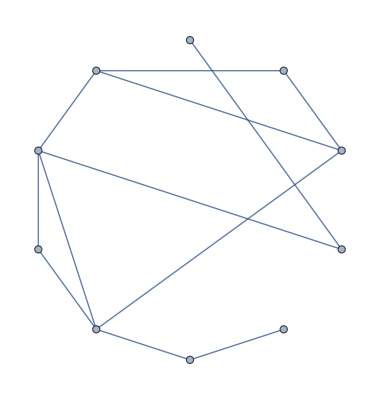
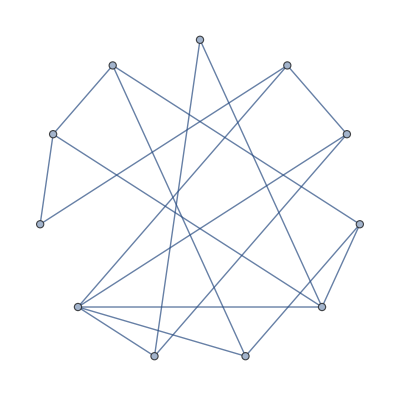
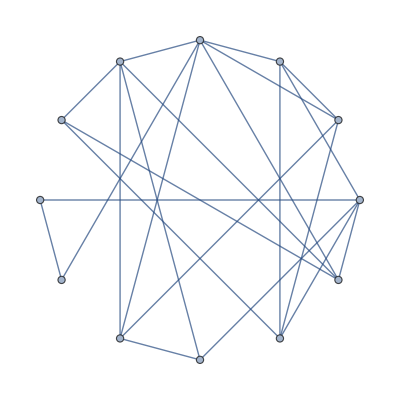
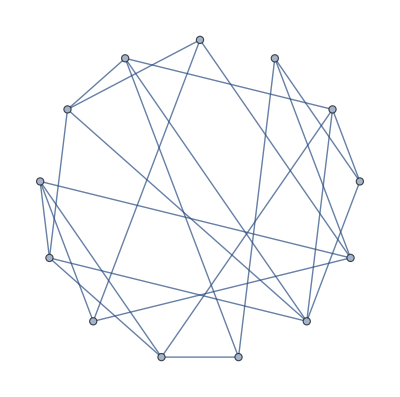
{-Graphics-{24,{{5,6,9}},12,21},-Graphics-{0,{{4,11,10}},17,28},-Graphics-{0,{{7,8,2}},23,36},-Graphics-{0,{{1,5,12}},24,45}}

```mathematica
Table[With[{edges=Avoiding[max]},With[{g=Graph[edges,GraphLayout->"CircularEmbedding"]},Labeled[g,{ChromaticPolynomial[EdgeDelete[CompleteGraph[max],edges],4],FindClique[g],Length[edges],Binomial[max,2]-(3*max-6)}]]],{max,10,13}]
```

```mathematica
Monitor[Table[{Binomial[max,2]-(3*max-6),Length[Avoiding[max]]},{max,5,13}],max]
```

{{1,1},{3,2},{6,6},{10,5},{15,11},{21,12},{28,15},{36,24},{45,25}}

```mathematica
SmartTake[list_,l_]:=If[Length[list]<l,list,Take[list,l]]
```

```mathematica
AvoidingComplete[length_,max_]:=Block[{all=Subsets[Range[length],{5}]},
Map[Last,Select[Flatten[AvoidingComplete[max,all,{}]],#=!=Null&]]
]
```

```mathematica
AvoidingComplete[max_,all_,result_]:=Block[{localresult,localall,localresults={},temp},
If[all=={},
1->result,
Table[
localresults=Table[
localresult=Append[result,UndirectedEdge[edge[[1]],edge[[2]]]];
localall=Select[all,Sort[Intersection[#,edge]]≠edge&];
{localresult,localall}
,
{edge,Subsets[tuple,{2}]}
];
temp=Tally[localresults,IsomorphicGraphQ[Graph[#1[[1]]],Graph[#2[[1]]]]&];
localresult=Map[First,temp];
Print[temp];
Interrupt[];
Table[
localall=var[[2]];
localresult=var[[1]];
AvoidingComplete[max,localall,localresult]
,{var,localresults}
]
,
{tuple,all}
]
]
]
```

```mathematica
AvoidingComplete[6,2]
```

{{1<->3,2<->4},{1<->3,2<->4},{1<->3,2<->4},{1<->4,2<->3},{1<->3,2<->4},{1<->4,2<->3},{2<->3,1<->4},{2<->3,1<->4},{2<->4,1<->3},{2<->4,1<->3}}

```mathematica
SelectFirst[AvoidingComplete[7,6],Length[#]==6&]
```

{1<->2,1<->3,2<->3}


-Graphics-{3,3}

```mathematica
With[{g=Graph[{1<->2,1<->3,2<->3}]},Labeled[CompleteGraph[VertexCount[g],GraphHighlight->EdgeList[GraphComplement[g]],GraphHighlightStyle->"Thick"],{3VertexCount[g]-6,EdgeCount[g]}]]
```

```mathematica
Map[Length,AvoidingComplete[6,2]]//Tally//Sort
```

{{2,6}}

```mathematica
Map[Length,AvoidingComplete[7,3]]//Tally//Sort
```

{{3,176400}}

```mathematica
Map[Length,AvoidingComplete[9,6]]//Tally//Sort
```

$Aborted

```mathematica
Map[Length,AvoidingComplete[10,7]]//Tally//Sort
```

$Aborted

```mathematica
Map[Length,AvoidingComplete[5]]//Tally//Sort
```

{{1,3}}

```mathematica
Map[Length,AvoidingComplete[6]]//Tally//Sort
```

{{2,4},{3,15}}

```mathematica
Map[Length,AvoidingComplete[7]]//Tally//Sort
```

{{3,7},{4,30},{5,78},{6,36}}

```mathematica
Map[Length,AvoidingComplete[8]]//Tally//Sort
```

{{4,3},{5,22},{6,174},{7,762},{8,1411},{9,1266},{10,351}}

```mathematica
Map[Length,AvoidingComplete[9]]//Tally//Sort
```

{{6,3},{7,68},{8,659},{9,4218},{10,17313},{11,39949},{12,54146},{13,41187},{14,16592},{15,2226}}

```mathematica
Map[Length,AvoidingComplete[10]]//Tally//Sort
```

{{9,45},{10,636},{11,6809},{12,53458},{13,298854},{14,1155345},{15,3075269},{16,5631953},{17,7103603},{18,6047109},{19,3293742},{20,1030711},{21,138525}}

```mathematica
Map[Length,AvoidingComplete[11]]//Tally//Sort
```

```mathematica
Map[Length,AvoidingComplete[11]]//Tally//Sort
```

$Aborted